```mathematica
worlddata=Import["https://covid.ourworldindata.org/data/owid-covid-data.csv"];
```

```mathematica
font="Helvetica Neue";
```

```mathematica
names={"Japan","Taiwan","Australia","United States","United Kingdom","India","France","Germany","Italy","New Zealand","Brazil","South Korea","Sweden","Thailand","China"};
namesLabel=names;
```

```mathematica
(*names={"Japan","Taiwan","Malaysia","Thailand","Vietnam","India","Indonesia","Mongolia","Singapore","Philippines","South Korea","China"};
namesLabel={"日本","台湾","マレーシア","タイ","ベトナム","インド","インドネシア","モンゴル","シンガポール","フィリピン","韓国","中国"}.08;
namesLabel=names;*)
```

```mathematica
font="Helvetica Neue";
fontsize=12;
```

```mathematica
startdate={2020,3,20};
enddate={2021,8,30};

tagoff=0.5;
startdateObj=DateObject[startdate];
date=4;
newDeathsSmoothedPerMillion=16;
newCasesSmoothedPerMillion=13;
newCasesSmoothed=7;
newCases=6;
elm=newDeathsSmoothedPerMillion;
title="new deathes smoothed per million";
pos0={0,0};
radius=Log[10]/Pi;
tag={0.001,0.01,0.1,1,10,100};
tagtext={0.001,0.01,0.1,1,10,100};
tagoff=0.5;
zeropx=-0.5
kmax=Length[names];
dataTmp=Table[Cases[worlddata,(x_)?(#1[[3]]==names[[k]]&)][[All,{date,elm,newCasesSmoothedPerMillion}]],{k,1,kmax}];
data=Table[DeleteCases[dataTmp[[k]],(x_)?(DateObject[#1[[1]]]<startdateObj&)],{k,1,kmax}];
colors=If[kmax==1,{Red},Table[ColorData["Rainbow"][(k-1)/(kmax-1)],{k,1,kmax}]];
minvalue=tag[[1]]/2;
maxvalue=3Last[tag];
```

-0.5

```mathematica
slopepos[val_,h_]:=pos0+{Cos[slopeangle]*val+h*Sin[slopeangle],(-Sin[slopeangle])*val+h*Cos[slopeangle]}
line[x_,val_]:=With[{angle=(val/Log[10])*Pi},{{x[[1]]+radius*Cos[-angle+Pi/2-slopeangle],x[[2]]+radius*Sin[-angle+Pi/2-slopeangle]},{x[[1]]-radius*Cos[-angle+Pi/2-slopeangle],x[[2]]-radius*Sin[-angle+Pi/2-slopeangle]}}];
```

```mathematica
slope:=Show[Graphics[Table[Text[Style[tagtext[[i]],10,Black,FontFamily->font],slopepos[Log[tag[[i]]],-tagoff]],{i,1,Length[tag]}]],Graphics[Text[Style[0,10,Black,FontFamily->font],slopepos[Log[minvalue],0]+{zeropx,-0.2}]],Graphics[Line[{slopepos[Log[minvalue],0],slopepos[Log[maxvalue],0]}]],Graphics[Line[{slopepos[Log[minvalue],0],slopepos[Log[minvalue],0]-{10,0}}]],Graphics[Table[Line[{slopepos[Log[tag[[i]]],0],slopepos[Log[tag[[i]]],-0.2]}],{i,1,Length[tag]}]],Graphics[Table[Table[Line[{slopepos[Log[k*tag[[i]]],0],slopepos[Log[k*tag[[i]]],-0.1]}],{k,1,10}],{i,1,Length[tag]-1}]]];
```

```mathematica
ball[val_,k_]:=Module[{pos,ang,tpos},
Show[
If[val≤minvalue,
cntzero++;
pos=slopepos[Log[minvalue],0]+{zeropx-cntzero*0.05,0}+{0,radius};
ang=-slopeangle/Pi Log[10] +(-cntzero*0.05) Cos[slopeangle];
tpos=slopepos[Log[minvalue],0]+{-cntzero*0.6,2.3radius},
pos=slopepos[Log[val],radius];
ang=Log[val];
tpos=slopepos[Log[val],2.3*radius]];
Graphics[{colors[[k]],Opacity[0.1],EdgeForm[{colors[[k]],Thickness[Medium]}],Disk[pos,radius]}],
Graphics[{colors[[k]],Line[line[pos,ang]]}],
Graphics[Rotate[Text[Style[namesLabel[[k]],12,colors[[k]],FontFamily->font],tpos,Left],π/6,tpos]]]]
```

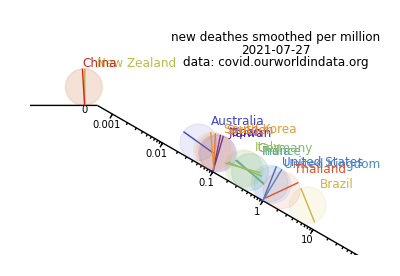
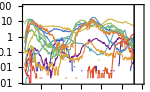

```mathematica
slopeangle=Pi/6;
tskip=0.5;
mainplotrange={{-9,4},{-2,7}};
posinset={-6,0};
textpos={0.5,6.5};
pltalldeath=DateListLogPlot[data[[All,All,2]]/.""->"0.",startdate,FrameStyle->Directive[9,Black,FontFamily->font],Frame->True,PlotStyle->Table[{Thickness[0.005],colors[[k]]},{k,1,kmax}],PlotRange->{{startdate,enddate},{0.001,100}},ImageSize->150];
output=
Table[cntzero=-1;plt=Show[pltalldeath,DateListLogPlot[{{DateObject[data[[1,i,1]]],10^-4},{DateObject[data[[1,i,1]]],10^8}},startdate,PlotStyle->{{Black,Thickness[0.007]}},Joined->True]];
Show[slope,Table[ball[data[[k,i,2]],k],{k,1,kmax}],
Graphics[Inset[Graphics[plt],posinset]],Graphics[Text[Style[title,fontsize,Black,FontFamily->font],textpos]],Graphics[Text[Style[data[[1,i,1]],fontsize,Black,FontFamily->font],textpos-{0,tskip}]],Graphics[Text[Style["data: covid.ourworldindata.org",fontsize,Black,FontFamily->font],textpos-{0,2tskip}]],
PlotRange->mainplotrange],{i,1,Length[data[[1]]]}];
outputMovie=Join[output,Table[Last[output],{j,1,30}]];
Last[outputMovie]
```

```mathematica
Export["~/world_death_per_M.mp4",outputMovie]
```

~/world_death_per_M.mp4

```mathematica
(*Export["~/asia_cases_per_M.mp4",outputMovie]*)
```

~/asia_cases_per_M.mp4